```mathematica
SetDirectory[NotebookDirectory[]];

gfactor=Import["g-factor","TSV"];
energy=Import["energies","TSV"];
```

```mathematica
gfactor[[1]][[2]]
```

569.765

```mathematica
energy//Dimensions
```

{30,21}

```mathematica
gfactor//Dimensions
energy//Dimensions
```

{50,5}

{50,21}

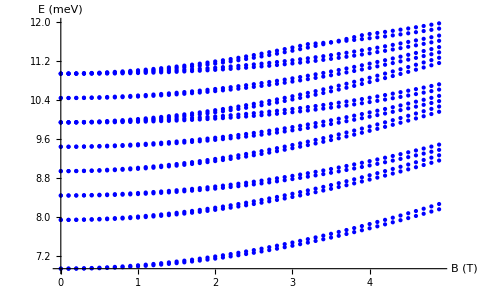

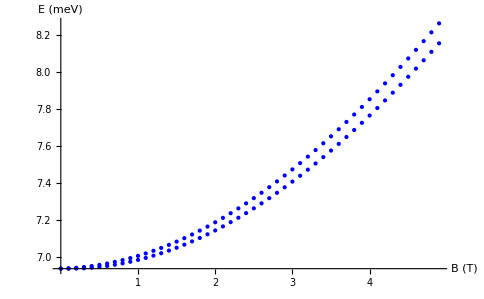

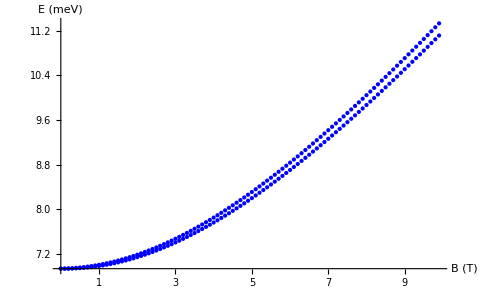

```mathematica
num=ListPlot[Table[Table[{(i-1)*1,energy[[i]][[j]]},{i,1,50}],{j,1,21}],PlotRange->All,PlotStyle->Blue,AxesLabel->{"B (T)","E (meV)"},Ticks->{{{0,"0"},{10,"1"},{20,"2"},{30,"3"},{40,"4"},{50,"5"}},Automatic}]

num1=ListPlot[Table[Table[{(i-1)*1,energy[[i]][[j]]},{i,1,50}],{j,1,2}],PlotRange->All,PlotStyle->Blue,AxesLabel->{"B (T)","E (meV)"},Ticks->{{{10,"1"},{20,"2"},{30,"3"},{40,"4"},{50,"5"}},Automatic}]

num2=ListPlot[Table[Table[{(i-1)*1,energy[[i]][[j]]},{i,1,100}],{j,1,2}],PlotRange->All,PlotStyle->Blue,AxesLabel->{"B (T)","E (meV)"},Ticks->{{{10,"1"},{20,"2"},{30,"3"},{40,"4"},{50,"5"},{60,"6"},{70,"7"},{80,"8"},{90,"9"},{100,"10"}},Automatic}]
```

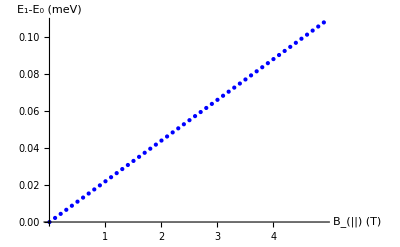

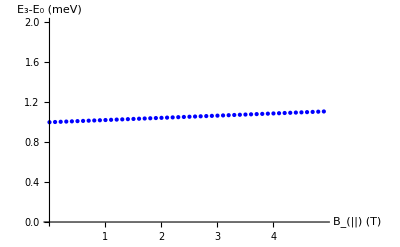

```mathematica
diff=ListPlot[Table[{(i-1)*1,energy[[i]][[2]]-energy[[i]][[1]]},{i,1,50}],PlotRange->All,PlotStyle->Blue,AxesLabel->{"B_(||) (T)","E_1-E_0 (meV)"},Ticks->{{{10,"1"},{20,"2"},{30,"3"},{40,"4"},{50,"5"}},Automatic}]

diff2=ListPlot[Table[{(i-1)*1,energy[[i]][[4]]-energy[[i]][[1]]},{i,1,50}],PlotRange->{0,2},PlotStyle->Blue,AxesLabel->{"B_(||) (T)","E_3-E_0 (meV)"},Ticks->{{{10,"1"},{20,"2"},{30,"3"},{40,"4"},{50,"5"}},Automatic}]
```

```mathematica
Table[{i,energy[[i]][[j]]},{j,1,20}]
```

{{10,6.97955},{10,6.99935},{10,7.97955},{10,7.99935},{10,8.47955},{10,8.49935},{10,8.97955},{10,8.99935},{10,9.47955},{10,9.49935},{10,9.97955},{10,9.97955},{10,9.99935},{10,9.99935},{10,10.4796},{10,10.4993},{10,10.9796},{10,10.9796},{10,10.9993},{10,10.9994}}

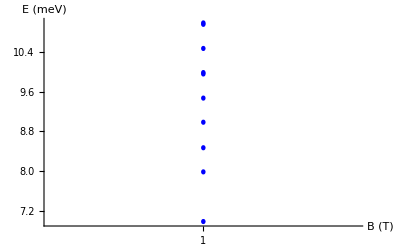

```mathematica
i=10;
ListPlot[Table[{i,energy[[i]][[j]]},{j,1,21}],PlotRange->All,PlotStyle->Blue,AxesLabel->{"B (T)","E (meV)"},Ticks->{{{10,"1"},{20,"2"},{30,"3"},{40,"4"},{50,"5"}},Automatic}]
```

```mathematica
lx =Sqrt[h^2/(1.602*10^-22*m)];
ly =Sqrt[h^2/(1.5*1.602*10^-22*m)];
(h^2/(m*lx^2))*10^19/1.602
h^2/(m*ly^2)*10^19/1.602
```

0.001

0.0015

```mathematica
Sqrt[h^2/(1.602*10^-22*m)]
```

3.37259×10^-8

```mathematica
Sqrt[h^2/(1.5*1.602*10^-22*m)]
```

2.7537×10^-8

```mathematica
(1+1.5)/2
```

1.25

```mathematica
h^2/(m*lB^2)*10^19/1.602*10^3
```

1.22489

```mathematica
wx=h/(m*lx^2);wy=h/(m*ly^2);wz[b_]:=h/(m*lz[b]^2);

b=10;
(((Bx[b,0]By[b,0] √wx √wy ee^2)/(8 wz[b]*m))*((ly^2 lz[b]^2)/(-ly^2+lz[b]^2)+(lx^2 lz[b]^2)/(-lx^2+lz[b]^2)))
```

0.

```mathematica
Bx[10,Pi/10]
```

√(5/8+(√5)/8)

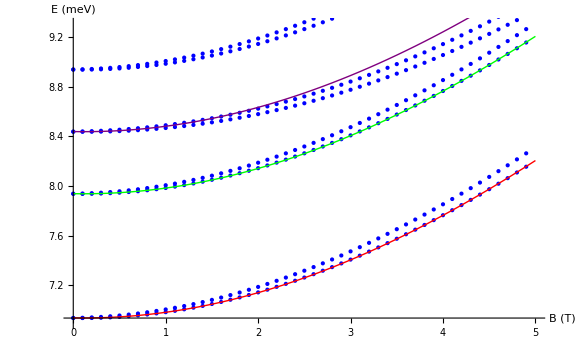

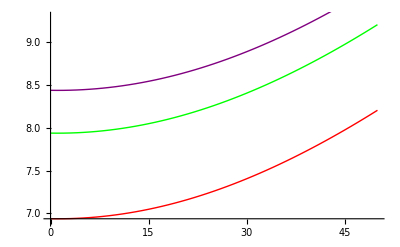

```mathematica
aa[b_]:=(-(ee^2 wx By[b,0]^2))/(4m wz[b])(lx^2 lz[b]^2)/(lx^2+lz[b]^2)-(ee^2 wy Bx[b,0]^2)/(4m wz[b])(ly^2 lz[b]^2)/(ly^2+lz[b]^2);
bb[b_]:=(ee^2 wx By[b,0]^2)/(4m wz[b])(lz[b]^2 lx^2)/(-lx^2+lz[b]^2)-(ee^2 Bx[b,0]^2 wy)/(4m*wz[b])(lz[b]^2 ly^2)/(lz[b]^2+ly^2);
cc[b_]:=(ee^2 Bx[b,0]^2 wy)/(4m wz[b])(ly^2 lz[b]^2)/(-ly^2+lz[b]^2)-(ee^2 By[b,0]^2 wx)/(4m*wz[b])(lz[b]^2 lx^2)/(lx^2+lz[b]^2);
dd[b_]:=(Bx[b,0]*By[b,0] √wx √wy ee^2)/(8 wz[b] m)((ly^2 lz[b]^2)/(-ly^2+lz[b]^2)+(lx^2 lz[b]^2)/(-lx^2+lz[b]^2))-(Bx[b,0]*By[b,0] √wx √wy ee^2)/(8 wz[b] m)((ly^2 lz[b]^2)/(ly^2+lz[b]^2)+(lx^2 lz[b]^2)/(lx^2+lz[b]^2));

E000[b_]:=h^2/(2m lz[b]^2)+h^2/(2m lx^2)+h^2/(2m ly^2);
E100[b_]:=h^2/(2m lz[b]^2)+(3 h^2)/(2m lx^2)+h^2/(2m ly^2);
E010[b_]:=h^2/(2m lz[b]^2)+h^2/(2m lx^2)+(3 h^2)/(2m ly^2);
μe=-2.04*10^(-24);
P000=ListPlot[Table[{b,(E000[b]+aa[b]+μe*b/10)*10^19/1.602*10^3},{b,0,50}],PlotStyle->Red,Joined->True];
P100=ListPlot[Table[{b,(E100[b]+bb[b]+μe*b/10)*10^19/1.602*10^3},{b,0,50}],PlotStyle->Green,Joined->True];
P010=ListPlot[Table[{b,(E010[b]+cc[b]+μe*b/10)*10^19/1.602*10^3},{b,0,50}],PlotStyle->Purple,Joined->True];
Show[{num,P000,P100,P010},PlotRange->{{0,50},{6.9,9.3}}]
Show[{P000,P100,P010},PlotRange->{{0,50},{6.9,9.3}}]
```

```mathematica
{b,aa[b]*10^19/1.602*10^3}
{b,1/2 (bb[b]+cc[b]+√((bb[b]-cc[b])^2+4 dd[b]^2))*10^19/1.602*10^3}
```

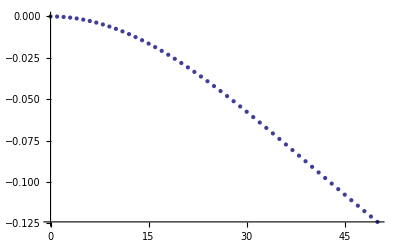

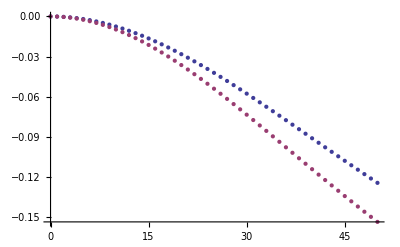

```mathematica
ListPlot[{Table[{b,aa[b]*10^19/1.602*10^3},{b,0,50}]}]
ListPlot[{Table[{b,bb[b]*10^19/1.602*10^3},{b,0,50}],Table[{b,cc[b]*10^19/1.602*10^3},{b,0,50}]}]
```

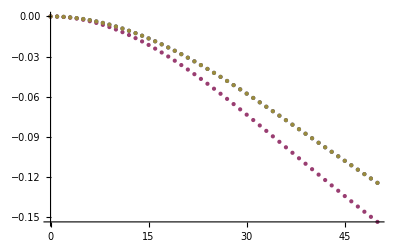

```mathematica
ListPlot[{Table[{b,aa[b]*10^19/1.602*10^3},{b,0,50}],Table[{b,1/2 (bb[b]+cc[b]-√((bb[b]-cc[b])^2+4 dd[b]^2))*10^19/1.602*10^3},{b,0,50}],Table[{b,1/2 (bb[b]+cc[b]+√((bb[b]-cc[b])^2+4 dd[b]^2))*10^19/1.602*10^3},{b,0,50}]}]
```

```mathematica
Eigensystem[({{aa, 0, 0}, {0, bb, dd}, {0, dd, cc}})]//FullSimplify
```

{{aa,1/2 (bb+cc-√((bb-cc)^2+4 dd^2)),1/2 (bb+cc+√((bb-cc)^2+4 dd^2))},{{1,0,0},{0,-(-bb+cc+√((bb-cc)^2+4 dd^2))/(2 dd),1},{0,(bb-cc+√((bb-cc)^2+4 dd^2))/(2 dd),1}}}

```mathematica
wx
```

1.5191×10^12

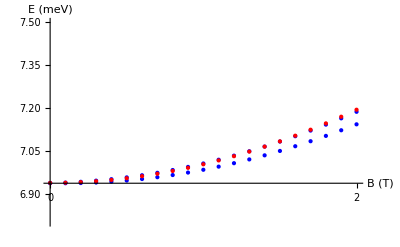

```mathematica
nopertur=ListPlot[Table[{b,(h^2/(2m lz[b]^2)+h^2/(2m lx^2)+h^2/(2m ly^2)-(((Bx[b,0]By[b,0] √wx √wy ee^2)/(8 wz[b]*m))*((ly^2 lz[b]^2)/(-ly^2+lz[b]^2)+(lx^2 lz[b]^2)/(-lx^2+lz[b]^2))-((Bx[b,0]By[b,0] √wx √wy ee^2)/(8 wz[b]*m))*((lx^2 lz[b]^2)/(lx^2+lz[b]^2)+(ly^2 lz[b]^2)/(ly^2+lz[b]^2))))*10^19/1.602*10^3},{b,0,49}],PlotRange->All,PlotStyle->Red];
Show[{num,nopertur},PlotRange->{{0,20},{6.8,7.5}}]
```

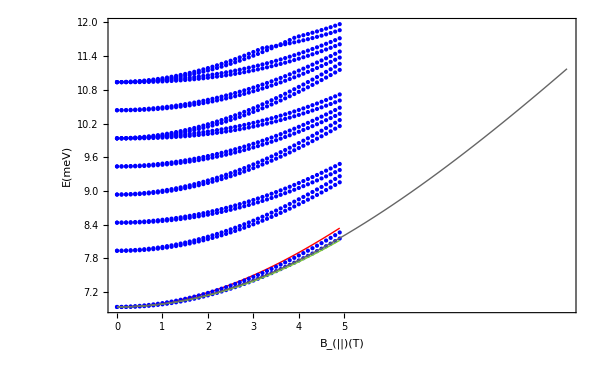

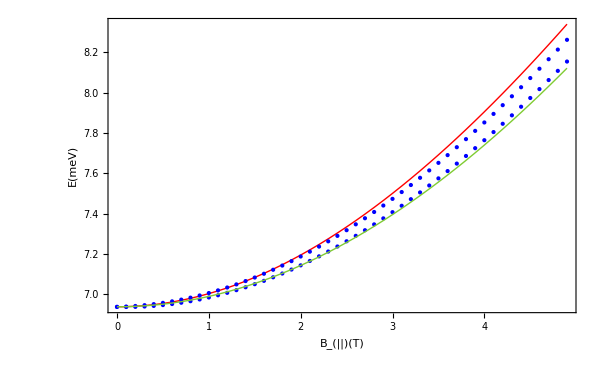

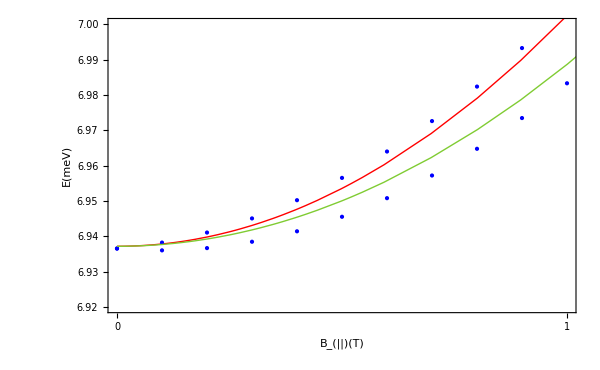

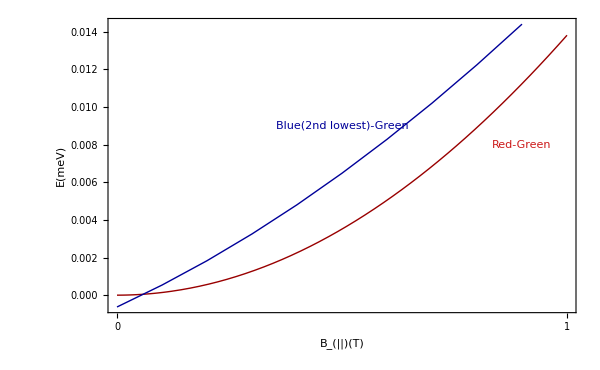

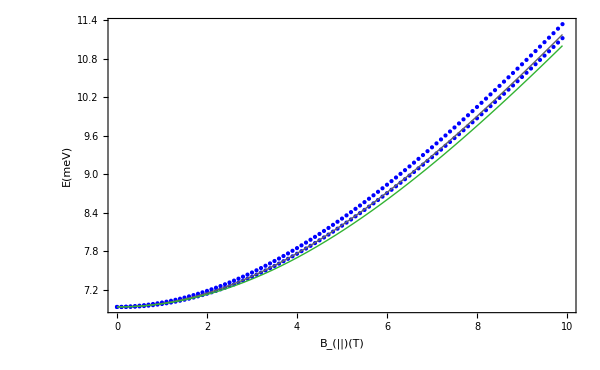

```mathematica
h=1.0545718*10^-34; (*hbar*)

m=0.067*9.10938356*10^-31; (* kg *)

l0=(30.473*10^-9); (* nm *)
lB=(l0^-4)^(-1/4); (*l0 -> L_0, not ten *)
lz[b_]:=((10*10^-9)^-4+(b/10)^2*((1.602*10^-19)^2)/h^2)^(-1/4);
ee=1.602*10^-19;
lx =Sqrt[h^2/(1.602*10^-22*m)];
ly =Sqrt[h^2/(1.5*1.602*10^-22*m)];




anaRed=Plot[(h^2/(m*(lz[b])^2)(1/2)+((h^2/(m*lx^2))+(h^2/(m*ly^2)))/2)*10^19/1.602*10^3,{b,0,49},PlotStyle->{Red,Thick}];(*(1+1.5)/2*)
anaGreen=Plot[((h^2/(m*(lz[b])^2)(1/2))+((h^2/(m*lx^2))+(h^2/(m*ly^2)))/2-(h^2/(m*lB^2)1/2((b/10)^2*((1.602*10^-19)^2)/h^2(lz[b])^4)))*10^19/1.602*10^3,{b,0,49},PlotStyle->{RGBColor[0.5,0.8,0.2],Thick}];
Bx[b_,ϕ_]:=(b/10)Cos[ϕ];
By[b_,ϕ_]:=(b/10)Sin[ϕ];
phi=Pi/2;

Heff[b_,ϕ_]:=m*lz[b]^4/(2 h^2)(-ee/m(Bx[b,ϕ](h/ly)-By[b,ϕ](h/lx)))^2;

ana3=Plot[((h^2/(m*(lz[b])^2)(1/2))-Heff[b,phi])*10^19/1.602*10^3+(1.5+1)/2,{b,0,99},PlotStyle->{RGBColor[0.4,0.4,0.4],Thick}]; (* re-derive *)

a=0;
ana4=Plot[((h^2/(m*(lz[b])^2)(1/2))-Heff[b,a])*10^19/1.602*10^3+(1.5+1)/2,{b,0,99},PlotStyle->{RGBColor[0.2,0.7,0.2],Thick}]; (* re-derive *)



anaRedmGreen=Plot[((h^2/(m*lB^2)1/2((b/10)^2*((1.602*10^-19)^2)/h^2(lz[b])^4)))*10^19/1.602*10^3,{b,0,10},PlotStyle->{RGBColor[0.6,-0.1,0],Thick}];(* gray *)
pow=Plot[((h^2/(m*lB^2)1/2((b/10)^2*((1.602*10^-19)^2)/h^2(10*10^-9)^4)))*10^19/1.602*10^3,{b,0,21},PlotStyle->{RGBColor[0.8,0.1,0.1],Thick}];


BluemGreen=ListPlot[Table[{(i-1)*1,energy[[i]][[2]]-(((h^2/(m*(lz[i-1])^2)(1/2))-(h^2/(m*lB^2)1/2(((i-1)/10)^2*((1.602*10^-19)^2)/h^2(lz[i-1])^4)))*10^19/1.602*10^3+(1+1.5)/2)},{i,1,10}],Joined->True,PlotStyle->{RGBColor[0,-0.1,0.6],Thick}];


Show[{anaRed,num,anaGreen,ana3},PlotRange->All,Frame->True,Axes->False,FrameTicks->{{{0,"0"},{10,"1"},{20,"2"},{30,"3"},{40,"4"},{50,"5"}},Automatic,None,None},FrameLabel->{"B_(||)(T)","E(meV)",None,None}]

Show[{anaRed,num1,anaGreen},PlotRange->All,Frame->True,Axes->False,FrameTicks->{{{0,"0"},{10,"1"},{20,"2"},{30,"3"},{40,"4"},{50,"5"}},Automatic,None,None},FrameLabel->{"B_(||)(T)","E(meV)",None,None}]

Show[{anaRed,num1,anaGreen},PlotRange->{{0,10},{6.92,7.0}},Frame->True,Axes->False,FrameTicks->{{{0,"0"},{10,"1"},{20,"2"},{30,"3"},{40,"4"},{50,"5"}},Automatic,None,None},FrameLabel->{"B_(||)(T)","E(meV)",None,None}]

Show[{anaRedmGreen,BluemGreen,Graphics[Text[Style["Red-Green",RGBColor[0.8,0.1,0.1]],{9,0.008}]],Graphics[Text[Style["Blue(2nd lowest)-Green",RGBColor[0,-0.1,0.6]],{5,0.009}]]},PlotRange->All,Frame->True,Axes->False,FrameTicks->{{{0,"0"},{10,"1"},{20,"2"},{30,"3"},{40,"4"},{50,"5"}},Automatic,None,None},FrameLabel->{"B_(||)(T)","E(meV)",None,None}]


Show[{num2,ana3,ana4},PlotRange->{{0,100},Automatic},Frame->True,Axes->False,FrameTicks->{{{0,"0"},{10,"1"},{20,"2"},{30,"3"},{40,"4"},{50,"5"},{60,"6"},{70,"7"},{80,"8"},{90,"9"},{100,"10"}},Automatic,None,None},FrameLabel->{"B_(||)(T)","E(meV)",None,None}]
```

```mathematica
Fit[Table[{(i-1)*1,((h^2/(m*lB^2)1/2(((i-1)/10)^2*((1.602*10^-19)^2)/h^2(lz[i-1])^4)))*10^19/1.602*10^3},{i,1,10}],{1,i,i^2,i^3,i^4,i^5,i^6,i^7,i^8},i]
Fit[Table[{(i-1)*1,energy[[i]][[2]]-(((h^2/(m*(lz[i-1])^2)(1/2))-(h^2/(m*lB^2)1/2(((i-1)/10)^2*((1.602*10^-19)^2)/h^2(lz[i-1])^4)))*10^19/1.602*10^3+(1+1.5)/2)},{i,1,10}],{1,i,i^2,i^3,i^4,i^5,i^6,i^7,i^8},i]
```

1.21402×10^-16-1.28288×10^-12 i+0.000141331 i^2-3.21886×10^-12 i^3-3.26129×10^-8 i^4-4.81285×10^-13 i^5+7.60913×10^-12 i^6-8.01614×10^-15 i^7-1.37813×10^-15 i^8

-0.000628816+0.00109979 i+0.000064933 i^2+8.08786×10^-13 i^3-1.9449×10^-8 i^4-5.78963×10^-14 i^5+5.05322×10^-12 i^6-3.36374×10^-15 i^7-1.04584×10^-15 i^8

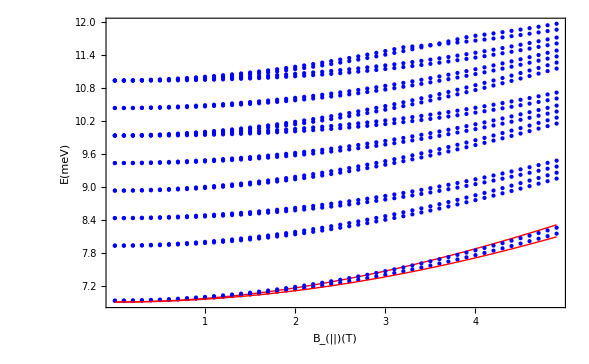

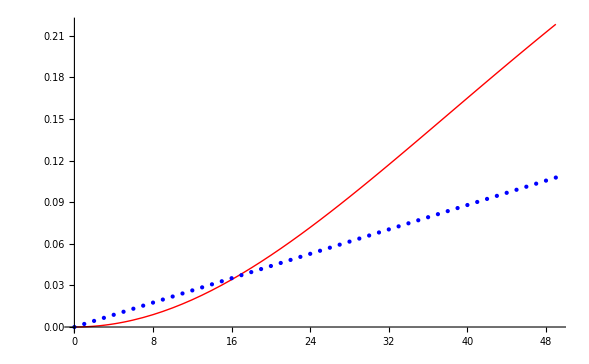

```mathematica
Show[{ana,num,ana2},PlotRange->All,Frame->True,Axes->False,FrameTicks->{{{10,"1"},{20,"2"},{30,"3"},{40,"4"},{50,"5"}},Automatic,None,None},FrameLabel->{"B_(||)(T)","E(meV)",None,None}]
Show[{ana1,diff}]
```

```mathematica
h^2/(0.067*10^-30*(32*10^-9)^2)10^19/1.6
```

0.000910972

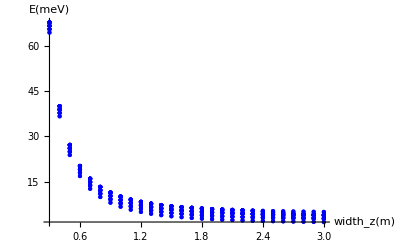

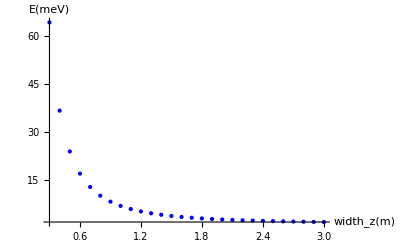

```mathematica
a=ListPlot[Table[Table[{(1+(i-1))*10^-9,energy[[i]][[j]]},{i,3,30}],{j,1,20}],PlotRange->All,PlotStyle->Blue,AxesLabel->{"width_z(m)","E(meV)"}]
d=ListPlot[Table[Table[{(1+(i-1))*10^-9,energy[[i]][[j]]},{i,3,30}],{j,1,1}],PlotRange->All,PlotStyle->Blue,AxesLabel->{"width_z(m)","E(meV)"}]
```

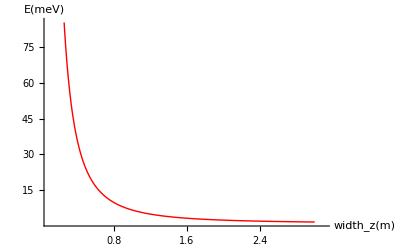

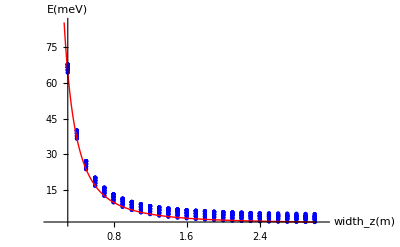

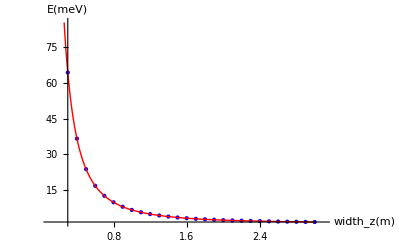

```mathematica
h=1.0545718*10^-34;

m=9.10938356*10^-31;b=Plot[(h^2/(2*0.067*m*x^2))*10^19/1.602*10^3+(h^2/(0.067*m*(32*10^-9)^2))*10^19/1.602*10^3,{x,2.6*10^-9,30*10^-9},PlotRange->{{1*10^-9,31*10^-9},All},PlotStyle->Red,AxesLabel->{"width_z(m)","E(meV)"}]
Show[{a,b},PlotRange->{{1*10^-9,31*10^-9},All}]
Show[{d,b},PlotRange->{{1*10^-9,31*10^-9},All}]
```

```mathematica
j=1;tab=Table[{(1+(i-1))*10^-9,energy[[i]][[j]]},{i,3,30}];
Table[tab[[i]][[2]],{i,1,28}]
x=9*10^-9;
Table[N[(h^2/(2*0.067*m*x^2))*10^19/1.602*10^3+(h^2/(0.067*m*(32*10^-9)^2))*10^19/1.602*10^3],{x,3*10^-9,30*10^-9,10^-9}]
```

{64.2944,36.6515,23.8568,16.9066,12.7158,9.99587,8.13107,6.79719,5.81027,5.05964,4.47547,4.01195,3.638,3.33196,3.07831,2.86576,2.68587,2.53229,2.40012,2.28556,2.18561,2.0979,2.0205,1.95186,1.8907,1.83598,1.78682,1.74249}

{64.3015,36.6556,23.8594,16.9085,12.7172,9.99697,8.13197,6.79794,5.81091,5.0602,4.47596,4.01239,3.6384,3.33232,3.07865,2.86607,2.68617,2.53257,2.40038,2.28581,2.18585,2.09813,2.02072,1.95207,1.89091,1.83618,1.78701,1.74268}

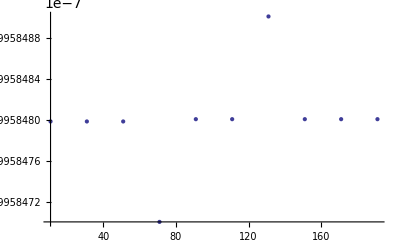

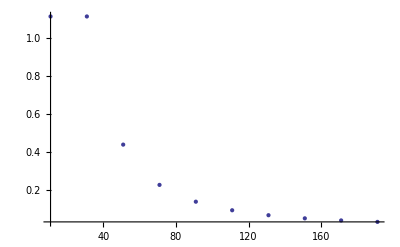

-Graphics-

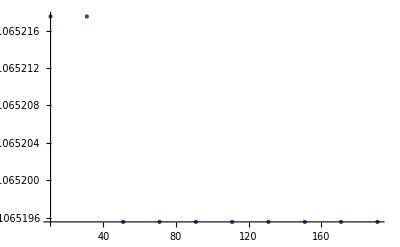

-Graphics-

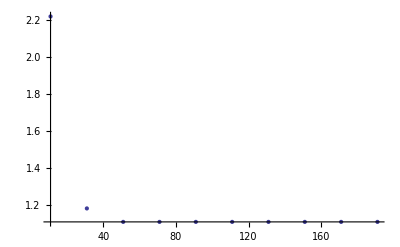

-Graphics-

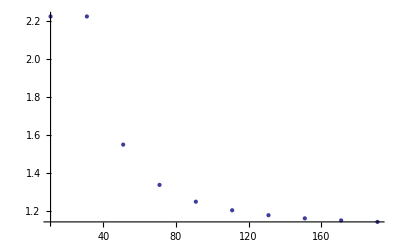

-Graphics-

-Graphics-

-Graphics-

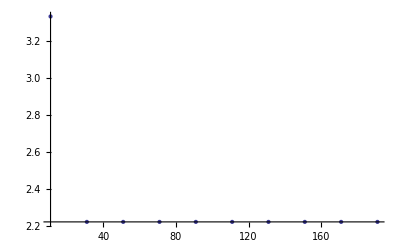

-Graphics-

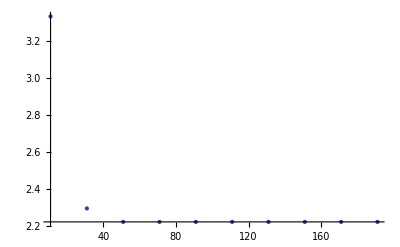

-Graphics-

-Graphics-

-Graphics-

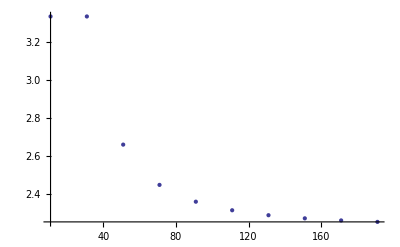

-Graphics-

-Graphics-

```mathematica
ListPlot[Table[{11+20(i-1),energy[[i]][[2]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[3]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[4]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[5]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[6]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[7]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[8]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[9]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[10]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[11]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[12]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[13]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]

ListPlot[Table[{11+20(i-1),energy[[i]][[14]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[15]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[16]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[17]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[18]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[19]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[20]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[21]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
```

```mathematica
gfactor
```

{{11.,5.81027,5.81027,2.19959×10^-7,0.38},{31.,1.70238,1.70238,2.19959×10^-7,0.38},{51.,1.32928,1.32928,2.19959×10^-7,0.38},{71.,1.22346,1.22346,2.19959×10^-7,0.38},{91.,1.17932,1.17932,2.19959×10^-7,0.38},{111.,1.15681,1.15681,2.19959×10^-7,0.38},{131.,1.14379,1.14379,2.19959×10^-7,0.38},{151.,1.13559,1.13559,2.19959×10^-7,0.38},{171.,1.1301,1.1301,2.19959×10^-7,0.38},{191.,1.12624,1.12624,2.19959×10^-7,0.38}}

```mathematica
energy
```

{{5.81027,5.81027,6.92092,6.92092,6.92092,6.92092,8.03157,8.03157,8.03157,8.03157,8.03157,8.03157,9.14223,9.14223,9.14223,9.14223,9.14223,9.14223,9.14223,9.14223,+5.81027059808228e+00 +5.81027081804076e+00 +6.92092255343186e+00 +6.92092255343220e+00 +6.92092277339026e+00 +6.92092277339071e+00 +8.03157416712175e+00 +8.03157429722056e+00 +8.03157438708016e+00 +8.03157451717906e+00 +8.03157463887307e+00 +8.03157485883149e+00 +9.14222644113477e+00 +9.14222644113484e+00 +9.14222666109304e+00 +9.14222666109331e+00 +9.14222822036243e+00 +9.14222822036248e+00 +9.14222844032071e+00 +9.14222844032103e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{1.70238,1.70238,2.81304,2.81304,2.81304,2.81304,2.88585,2.88585,3.92369,3.92369,3.92369,3.92369,3.92369,3.92369,3.9965,3.9965,3.9965,3.9965,5.03434,5.03434,+1.70238331514979e+00 +1.70238353510827e+00 +2.81303527049955e+00 +2.81303527049958e+00 +2.81303549045804e+00 +2.81303549045805e+00 +2.88584608013666e+00 +2.88584630009514e+00 +3.92368688418915e+00 +3.92368701428806e+00 +3.92368710414761e+00 +3.92368723424651e+00 +3.92368735594046e+00 +3.92368757589897e+00 +3.99649803548641e+00 +3.99649803548645e+00 +3.99649825544490e+00 +3.99649825544492e+00 +5.03433915820228e+00 +5.03433937816075e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{1.32928,1.32928,1.76654,1.76654,2.43993,2.43993,2.43993,2.43993,2.87719,2.87719,2.87719,2.87719,3.55058,3.55058,3.55058,3.55058,3.55058,3.55059,3.98784,3.98784,+1.32928086728138e+00 +1.32928108723986e+00 +1.76653873653139e+00 +1.76653895648983e+00 +2.43993282263110e+00 +2.43993282263120e+00 +2.43993304258954e+00 +2.43993304258970e+00 +2.87719069188109e+00 +2.87719069188112e+00 +2.87719091183956e+00 +2.87719091183961e+00 +3.55058443632067e+00 +3.55058456641961e+00 +3.55058465627915e+00 +3.55058478637807e+00 +3.55058490807199e+00 +3.55058512803050e+00 +3.98784230557064e+00 +3.98784243566955e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{1.22346,1.22346,1.44907,1.44907,2.33411,2.33411,2.33411,2.33411,2.55972,2.55972,2.55972,2.55972,3.44476,3.44476,3.44476,3.44476,3.44476,3.44476,3.67037,3.67037,+1.22345769742200e+00 +1.22345791738047e+00 +1.44906922695321e+00 +1.44906944691161e+00 +2.33410965277170e+00 +2.33410965277176e+00 +2.33410987273018e+00 +2.33410987273028e+00 +2.55972118230284e+00 +2.55972118230297e+00 +2.55972140226132e+00 +2.55972140226142e+00 +3.44476126646138e+00 +3.44476139656024e+00 +3.44476148641974e+00 +3.44476161651870e+00 +3.44476173821260e+00 +3.44476195817121e+00 +3.67037279599244e+00 +3.67037292609140e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{1.17932,1.17932,1.31666,1.31666,2.28997,2.28997,2.28997,2.28997,2.42731,2.42731,2.42731,2.42731,3.40063,3.40063,3.40063,3.40063,3.40063,3.40063,3.53796,3.53796,+1.17932164199292e+00 +1.17932186195140e+00 +1.31666106066603e+00 +1.31666128062455e+00 +2.28997359734267e+00 +2.28997359734274e+00 +2.28997381730120e+00 +2.28997381730122e+00 +2.42731301601577e+00 +2.42731301601584e+00 +2.42731323597427e+00 +2.42731323597430e+00 +3.40062521103231e+00 +3.40062534113113e+00 +3.40062543099075e+00 +3.40062556108965e+00 +3.40062568278360e+00 +3.40062590274212e+00 +3.53796462970534e+00 +3.53796475980430e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{1.15681,1.15681,1.24911,1.24911,2.26746,2.26746,2.26746,2.26746,2.35976,2.35976,2.35976,2.35976,3.37811,3.37811,3.37811,3.37811,3.37811,3.37811,3.47042,3.47042,+1.15680515629716e+00 +1.15680537625564e+00 +1.24911160357878e+00 +1.24911182353728e+00 +2.26745711164689e+00 +2.26745711164694e+00 +2.26745733160538e+00 +2.26745733160541e+00 +2.35976355892850e+00 +2.35976355892854e+00 +2.35976377888697e+00 +2.35976377888704e+00 +3.37810872533655e+00 +3.37810885543537e+00 +3.37810894529490e+00 +3.37810907539389e+00 +3.37810919708781e+00 +3.37810941704636e+00 +3.47041517261814e+00 +3.47041530271696e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{1.14379,1.14379,1.21006,1.21006,2.25444,2.25444,2.25444,2.25444,2.32071,2.32071,2.32071,2.32071,3.36509,3.36509,3.36509,3.36509,3.36509,3.36509,3.43136,3.43136,+1.14378833949995e+00 +1.14378855945844e+00 +1.21006115318717e+00 +1.21006137314566e+00 +2.25444029484974e+00 +2.25444029484976e+00 +2.25444051480822e+00 +2.25444051480822e+00 +2.32071310853689e+00 +2.32071310853690e+00 +2.32071332849538e+00 +2.32071332849539e+00 +3.36509190853924e+00 +3.36509203863818e+00 +3.36509212849772e+00 +3.36509225859665e+00 +3.36509238029061e+00 +3.36509260024903e+00 +3.43136472222643e+00 +3.43136485232532e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{1.13559,1.13559,1.18547,1.18547,2.24624,2.24624,2.24624,2.24624,2.29612,2.29612,2.29612,2.29612,3.3569,3.3569,3.3569,3.3569,3.3569,3.3569,3.40678,3.40678,+1.13559179900584e+00 +1.13559201896432e+00 +1.18547153170479e+00 +1.18547175166328e+00 +2.24624375435561e+00 +2.24624375435562e+00 +2.24624397431410e+00 +2.24624397431410e+00 +2.29612348705457e+00 +2.29612348705458e+00 +2.29612370701308e+00 +2.29612370701309e+00 +3.35689536804517e+00 +3.35689549814407e+00 +3.35689558800362e+00 +3.35689571810250e+00 +3.35689583979653e+00 +3.35689605975503e+00 +3.40677510074413e+00 +3.40677523084301e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{1.1301,1.1301,1.16899,1.16899,2.24075,2.24075,2.24075,2.24075,2.27965,2.27965,2.27965,2.27965,3.3514,3.3514,3.3514,3.3514,3.3514,3.3514,3.3903,3.3903,+1.13009907586726e+00 +1.13009929582574e+00 +1.16899336228901e+00 +1.16899358224752e+00 +2.24075103121700e+00 +2.24075103121704e+00 +2.24075125117551e+00 +2.24075125117552e+00 +2.27964531763881e+00 +2.27964531763881e+00 +2.27964553759728e+00 +2.27964553759730e+00 +3.35140264490657e+00 +3.35140277500548e+00 +3.35140286486498e+00 +3.35140299496394e+00 +3.35140311665790e+00 +3.35140333661640e+00 +3.39029693132838e+00 +3.39029706142723e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{1.12624,1.12624,1.15741,1.15742,2.23689,2.23689,2.23689,2.23689,2.26807,2.26807,2.26807,2.26807,3.34754,3.34754,3.34754,3.34754,3.34754,3.34754,3.37872,3.37872,+1.12623960694867e+00 +1.12623982690715e+00 +1.15741495553324e+00 +1.15741517549174e+00 +2.23689156229842e+00 +2.23689156229843e+00 +2.23689178225689e+00 +2.23689178225693e+00 +2.26806691088298e+00 +2.26806691088298e+00 +2.26806713084147e+00 +2.26806713084148e+00 +3.34754317598798e+00 +3.34754330608688e+00 +3.34754339594642e+00 +3.34754352604533e+00 +3.34754364773927e+00 +3.34754386769782e+00 +3.37871852457253e+00 +3.37871865467144e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 }}

```mathematica
Table[{11+20(i-1),energy[[i]][[21]]-energy[[i]][[1]]},{i,1,10}]
```

{{11,-5.81027++5.81027059808228e+00 +5.81027081804076e+00 +6.92092255343186e+00 +6.92092255343220e+00 +6.92092277339026e+00 +6.92092277339071e+00 +8.03157416712175e+00 +8.03157429722056e+00 +8.03157438708016e+00 +8.03157451717906e+00 +8.03157463887307e+00 +8.03157485883149e+00 +9.14222644113477e+00 +9.14222644113484e+00 +9.14222666109304e+00 +9.14222666109331e+00 +9.14222822036243e+00 +9.14222822036248e+00 +9.14222844032071e+00 +9.14222844032103e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{31,-1.70238++1.70238331514979e+00 +1.70238353510827e+00 +2.81303527049955e+00 +2.81303527049958e+00 +2.81303549045804e+00 +2.81303549045805e+00 +2.88584608013666e+00 +2.88584630009514e+00 +3.92368688418915e+00 +3.92368701428806e+00 +3.92368710414761e+00 +3.92368723424651e+00 +3.92368735594046e+00 +3.92368757589897e+00 +3.99649803548641e+00 +3.99649803548645e+00 +3.99649825544490e+00 +3.99649825544492e+00 +5.03433915820228e+00 +5.03433937816075e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{51,-1.32928++1.32928086728138e+00 +1.32928108723986e+00 +1.76653873653139e+00 +1.76653895648983e+00 +2.43993282263110e+00 +2.43993282263120e+00 +2.43993304258954e+00 +2.43993304258970e+00 +2.87719069188109e+00 +2.87719069188112e+00 +2.87719091183956e+00 +2.87719091183961e+00 +3.55058443632067e+00 +3.55058456641961e+00 +3.55058465627915e+00 +3.55058478637807e+00 +3.55058490807199e+00 +3.55058512803050e+00 +3.98784230557064e+00 +3.98784243566955e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{71,-1.22346++1.22345769742200e+00 +1.22345791738047e+00 +1.44906922695321e+00 +1.44906944691161e+00 +2.33410965277170e+00 +2.33410965277176e+00 +2.33410987273018e+00 +2.33410987273028e+00 +2.55972118230284e+00 +2.55972118230297e+00 +2.55972140226132e+00 +2.55972140226142e+00 +3.44476126646138e+00 +3.44476139656024e+00 +3.44476148641974e+00 +3.44476161651870e+00 +3.44476173821260e+00 +3.44476195817121e+00 +3.67037279599244e+00 +3.67037292609140e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{91,-1.17932++1.17932164199292e+00 +1.17932186195140e+00 +1.31666106066603e+00 +1.31666128062455e+00 +2.28997359734267e+00 +2.28997359734274e+00 +2.28997381730120e+00 +2.28997381730122e+00 +2.42731301601577e+00 +2.42731301601584e+00 +2.42731323597427e+00 +2.42731323597430e+00 +3.40062521103231e+00 +3.40062534113113e+00 +3.40062543099075e+00 +3.40062556108965e+00 +3.40062568278360e+00 +3.40062590274212e+00 +3.53796462970534e+00 +3.53796475980430e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{111,-1.15681++1.15680515629716e+00 +1.15680537625564e+00 +1.24911160357878e+00 +1.24911182353728e+00 +2.26745711164689e+00 +2.26745711164694e+00 +2.26745733160538e+00 +2.26745733160541e+00 +2.35976355892850e+00 +2.35976355892854e+00 +2.35976377888697e+00 +2.35976377888704e+00 +3.37810872533655e+00 +3.37810885543537e+00 +3.37810894529490e+00 +3.37810907539389e+00 +3.37810919708781e+00 +3.37810941704636e+00 +3.47041517261814e+00 +3.47041530271696e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{131,-1.14379++1.14378833949995e+00 +1.14378855945844e+00 +1.21006115318717e+00 +1.21006137314566e+00 +2.25444029484974e+00 +2.25444029484976e+00 +2.25444051480822e+00 +2.25444051480822e+00 +2.32071310853689e+00 +2.32071310853690e+00 +2.32071332849538e+00 +2.32071332849539e+00 +3.36509190853924e+00 +3.36509203863818e+00 +3.36509212849772e+00 +3.36509225859665e+00 +3.36509238029061e+00 +3.36509260024903e+00 +3.43136472222643e+00 +3.43136485232532e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{151,-1.13559++1.13559179900584e+00 +1.13559201896432e+00 +1.18547153170479e+00 +1.18547175166328e+00 +2.24624375435561e+00 +2.24624375435562e+00 +2.24624397431410e+00 +2.24624397431410e+00 +2.29612348705457e+00 +2.29612348705458e+00 +2.29612370701308e+00 +2.29612370701309e+00 +3.35689536804517e+00 +3.35689549814407e+00 +3.35689558800362e+00 +3.35689571810250e+00 +3.35689583979653e+00 +3.35689605975503e+00 +3.40677510074413e+00 +3.40677523084301e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{171,-1.1301++1.13009907586726e+00 +1.13009929582574e+00 +1.16899336228901e+00 +1.16899358224752e+00 +2.24075103121700e+00 +2.24075103121704e+00 +2.24075125117551e+00 +2.24075125117552e+00 +2.27964531763881e+00 +2.27964531763881e+00 +2.27964553759728e+00 +2.27964553759730e+00 +3.35140264490657e+00 +3.35140277500548e+00 +3.35140286486498e+00 +3.35140299496394e+00 +3.35140311665790e+00 +3.35140333661640e+00 +3.39029693132838e+00 +3.39029706142723e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{191,-1.12624++1.12623960694867e+00 +1.12623982690715e+00 +1.15741495553324e+00 +1.15741517549174e+00 +2.23689156229842e+00 +2.23689156229843e+00 +2.23689178225689e+00 +2.23689178225693e+00 +2.26806691088298e+00 +2.26806691088298e+00 +2.26806713084147e+00 +2.26806713084148e+00 +3.34754317598798e+00 +3.34754330608688e+00 +3.34754339594642e+00 +3.34754352604533e+00 +3.34754364773927e+00 +3.34754386769782e+00 +3.37871852457253e+00 +3.37871865467144e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 }}

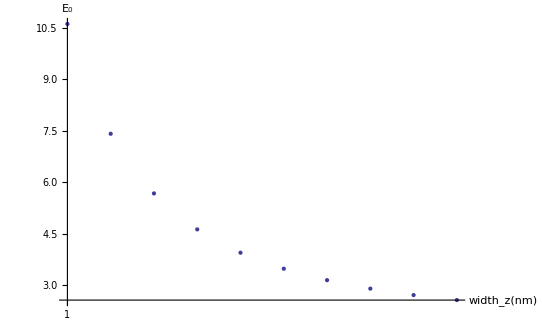

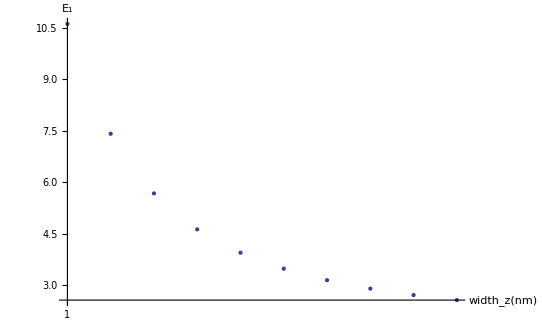

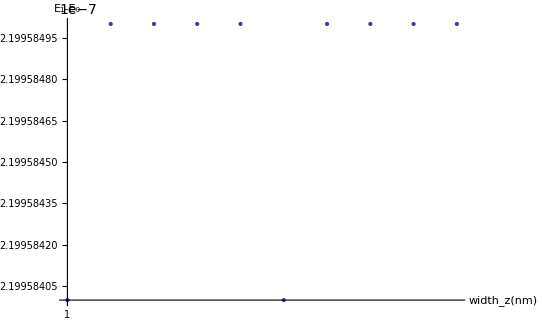

```mathematica
ListPlot[Table[gfactor[[i]][[2]],{i,1,10}],Ticks->{{{1,"1"},{25,"50"},{50,"100"}},Automatic},AxesLabel->{"width_z(nm)","E_0"},PlotRange->All]

ListPlot[Table[gfactor[[i]][[3]],{i,1,10}],Ticks->{{{1,"1"},{25,"50"},{50,"100"}},Automatic},AxesLabel->{"width_z(nm)","E_1"},PlotRange->All]

ListPlot[Table[gfactor[[i]][[4]],{i,1,10}],Ticks->{{{1,"1"},{25,"50"},{50,"100"}},Automatic},AxesLabel->{"width_z(nm)","E_1-E_0"},PlotRange->All]
```

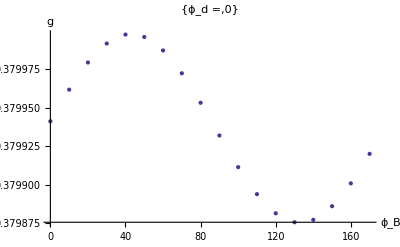
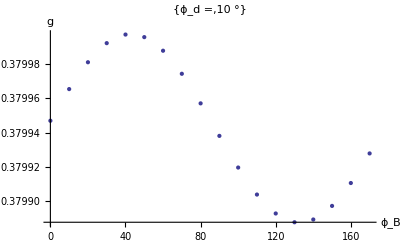
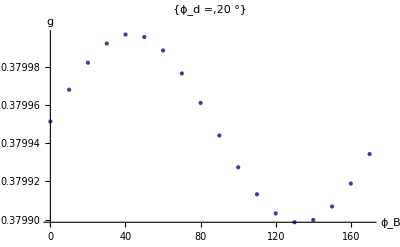
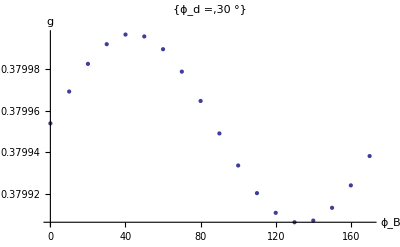
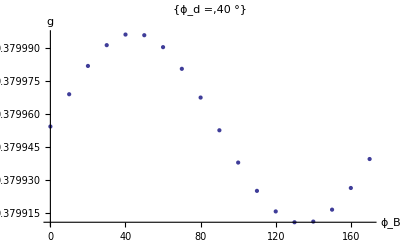
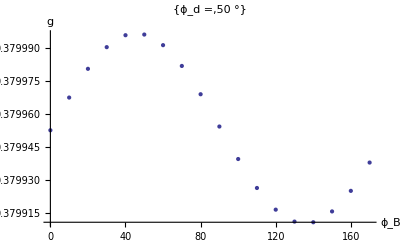
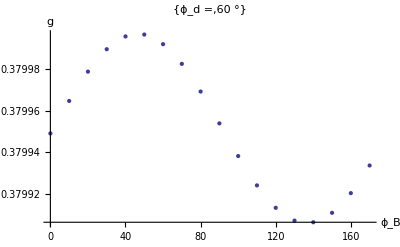
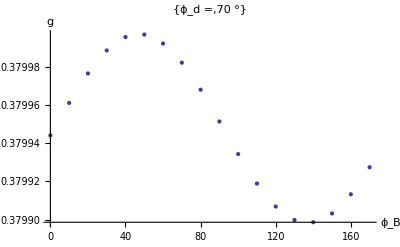

```mathematica
Table[ListPlot[Table[{gfactor[[i]][[1]],gfactor[[i]][[5]]},{i,1+18*j,18+18*j}],AxesLabel->{"ϕ_B","g"},PlotLabel->{"ϕ_d =",j*10 "°"}],{j,0,17}]
```

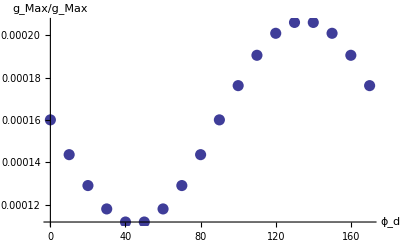

```mathematica
ListPlot[Table[{j*10,(Max[Table[gfactor[[i]][[5]],{i,1+18*j,18+18*j}]]-Min[Table[gfactor[[i]][[5]],{i,1+18*j,18+18*j}]])/(Max[Table[gfactor[[i]][[5]],{i,1+18*j,18+18*j}]]+Min[Table[gfactor[[i]][[5]],{i,1+18*j,18+18*j}]])},{j,0,17}],AxesLabel->{"ϕ_d","g_Max/g_Max"},PlotStyle->Directive[PointSize->0.02]]
```